```mathematica
Needs["SpectralBP`"];
```

# SpectralBP - Quantum Mechanics

In this notebook, we show how SpectralBP can be used in solving problems in quantum mechanics. We choose two very standard problems, the infinite square well potential and the harmonic potential. We also feature how well SpectralBP solves perturbations, nonanalytic solutions, and anharmonic potentials.

## Infinite Square Well

## Basic commands

Recall the time-independent Schrodinger equation:

```mathematica
TISE := (energy - V[x])ψ[x] +1/2 ψ''[x];
```

Here we have set both ℏ and the mass to 1. For the infinite square well, whose infinite barriers we define to be located at x = 0 and x = 1, the potential in the domain of the solution vanishes

```mathematica
V[x_] := 0;
```

The simplest command in SpectralBP is GetModes[eqn, N]. The first input eqn is the equation you wish to solve the eigenvalues for, and the second input N specifies the order of the Bernstein polynomial basis one uses in the pseudospectral method discussed in the paper.

As discussed in the paper, BPs are uniquely qualified in handling boundary value problems we encounter in quantum mechanics. For example, in the infinite square well potential, the solution must vanish at x = 0 and x = 1. Which is to say that ψ[x→0] ∼ x and ψ[x→1] ∼ (1-x), at the very least. 

This is enforced by two options, LBPower and UBPower, which specifies the exponent of the leading polynomial expansion at the lower and upper bound respectively. These two options default to zero, so we must change them both to 1.

```mathematica
modes1 = GetModes[TISE,50,LBPower->1,UBPower->1];//Timing
```

{1.26563,Null}

Recall that the expected eigenvalues for the energy is of the form (n^2 π^2)/2. To print the frequencies on the complex plane, we use the function PrintFrequencies[spectrum]. We may control how many eigenvalues are plotted, by using the options NSpectrum. We may also specify the name of our eigenvalue, using FreqName. In the following command, we show the first 10 eigenvalues.

These two options default to -1 (which shows the entire spectrum) and ω respectively.

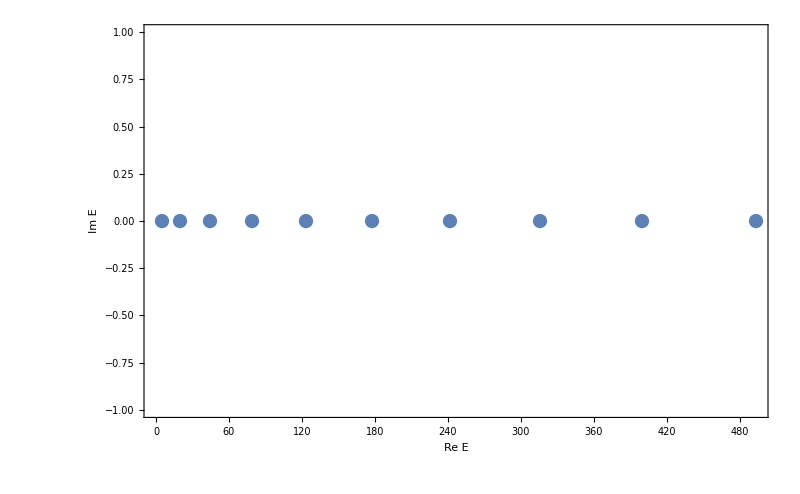

```mathematica
PrintFrequencies[modes1,NSpectrum->10,FreqName->"E"]
```

When divided by π^2/2, the resulting eigenvalues should be squares of integers, which we verify:

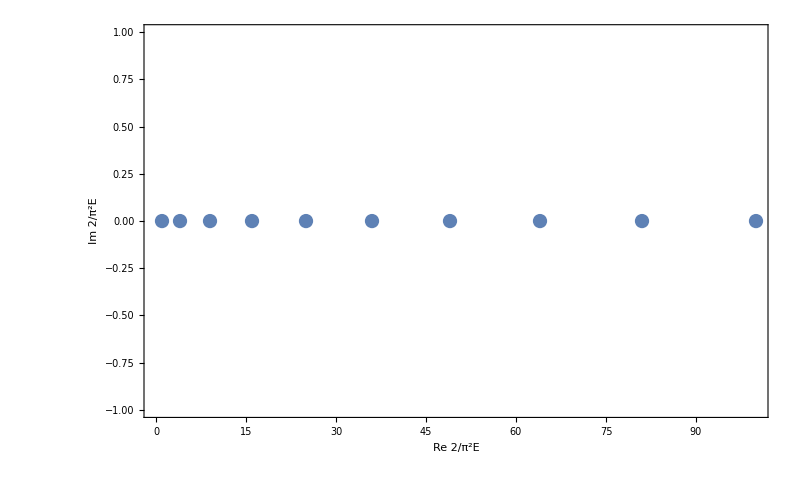

```mathematica
PrintFrequencies[(2*modes1)/π^2,NSpectrum->10,FreqName->"2/π^2E"]
```

One may also print out the eigenfunctions corresponding to each eigenvalue, using PrintEigenfunctions[eqn,spectrum,N]. We must also input all relevant information to construct the matrix equation from which we calculated our eigenvalues.

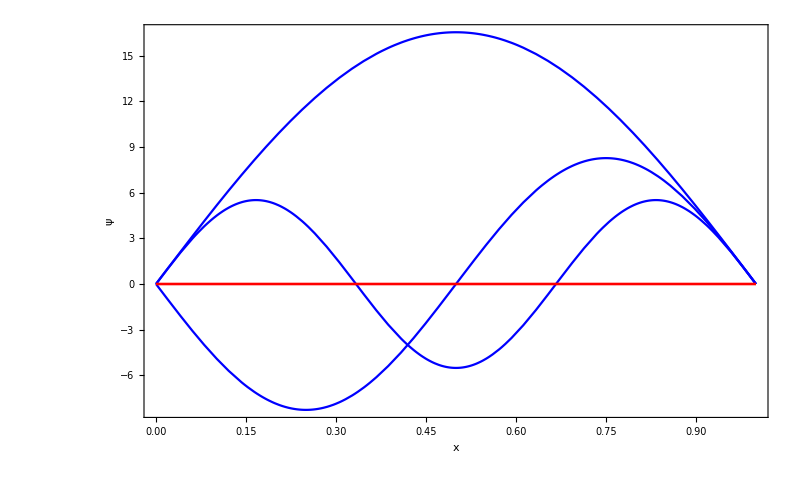

```mathematica
PrintEigenfunctions[TISE,modes1⟦1;;3⟧,50,LBPower->1,UBPower->1]
```

By default, the eigenfunctions are normalized by setting the coefficient of the leading polynomial expansion at the upper bound to 1. In this case, the eigenfunctions are normalized such that ψ[x→1] ∼ (1-u).

This is controlled by the option Normalization, which defaults to “UB” for upper bound. One may also set this to “LB”. There is also the option to normalize it with respect to the integral of the square of the function.

To normalize with respect to the square integral, we set Normalization → “L2Norm”.

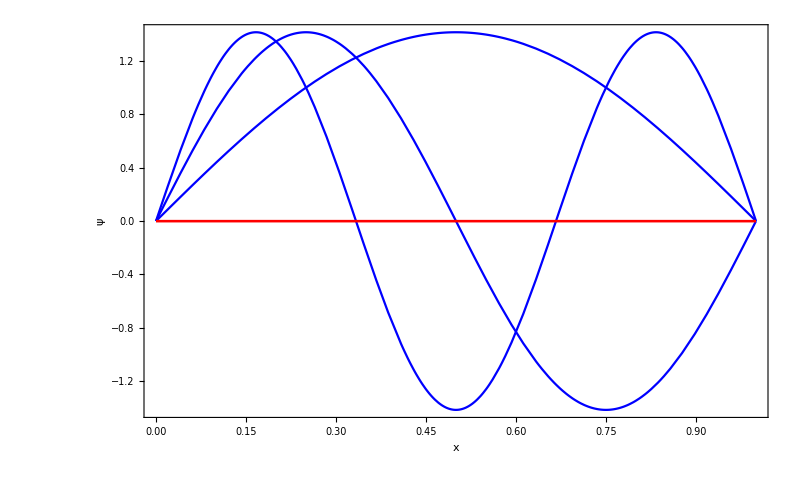

```mathematica
PrintEigenfunctions[TISE,modes1⟦1;;3⟧,50,LBPower->1,UBPower->1,Normalization->"L2Norm"]
```

We may also calculate two spectra using two different BP polynomial orders, and use the command CompareModes[spectrum1, spectrum2] to filter out the eigenvalues not common to both spectra. There are two default options, Cutoff → 3 and TestMagnitude → True. It returns a list {eigenhigh, eigenlow}, where the list eigenhigh comes from the spectrum calculated from a higher BP order.

```mathematica
modes2 = GetModes[TISE,80,LBPower->1,UBPower->1];
convergedmodes = CompareModes[modes1,modes2];
```

One can then use the command PrintTable[{eigenhigh,eigenlow}] to print a table of frequencies, formatting the eigenvalues up to the digit they agree in. As it is a print function, one can also change the eigenvalue name using FreqName

```mathematica
PrintTable[(2*convergedmodes)/π^2,FreqName->"2/π^2E"]
```

Real Eigenvalues |  | 
n | Re 2/π^2E | Im 2/π^2E
1 | 1. | 0
2 | 4. | 0
3 | 9. | 0
4 | 16. | 0
5 | 25. | 0
6 | 36. | 0
7 | 49. | 0
8 | 64. | 0
9 | 81. | 0
10 | 100. | 0
11 | 121. | 0
12 | 144. | 0
13 | 169. | 0
14 | 196. | 0
15 | 225. | 0
16 | 256. | 0
17 | 289. | 0
18 | 324. | 0
19 | 361. | 0
20 | 400. | 0
21 | 441. | 0
22 | 484. | 0
23 | 529. | 0
24 | 576. | 0
25 | 625. | 0
26 | 676. | 0
27 | 729. | 0
28 | 784. | 0

One can quickly do all the above using two functions: GetAccurateModes[eqn,N1,N2] and PrintAll[eqn,{eigenhigh,eigenlow},N1]. A new option available is NEigenFunc, which specifies how many eigenfunctions are printed.

```mathematica
quickmodes = GetAccurateModes[TISE,50,80,LBPower->1,UBPower->1];
PrintAll[TISE,quickmodes,50,LBPower->1,UBPower->1,NSpectrum->10,NEigenFunc->3,Normalization->"L2Norm",FreqName->"E"]
```

Eigenvalues
-Graphics-
Table of Eigenvalues
Real Eigenvalues |  | 
n | Re E | Im E
1 | 4.93480220054467930942 | 0
2 | 19.73920880217871723767 | 0
3 | 44.41321980490211378476 | 0
4 | 78.95683520871486895068 | 0
5 | 123.370055013616982735431 | 0
6 | 177.65287921960845513902 | 0
7 | 241.80530782668928616145 | 0
8 | 315.8273408348594758027 | 0
9 | 399.7189782441190240628 | 0
10 | 493.48022005446793094172 | 0
11 | 597.11106626590619643949 | 0
12 | 710.61151687843382056 | 0
13 | 833.9815718920508033 | 0
14 | 967.22123130675714 | 0
15 | 1110.3304951225528 | 0
16 | 1263.30936333944 | 0
17 | 1426.1578359574 | 0
18 | 1598.875912976 | 0
19 | 1781.4635944 | 0
20 | 1973.9208802 | 0
21 | 2176.24777 | 0
22 | 2388.44427 | 0
23 | 2610.5104 | 0
24 | 2842.4461 | 0
25 | 3084.251 | 0
26 | 3335.93 | 0
27 | 3597.5 | 0
28 | 3869. | 0
Undamped Eigenfunctions
{-Graphics-}

## A Note On Machine Precision

By default, the calculation of eigenvalues using a BP order N is done with a machine precision N/2. For the TISE, this is adequate as there is only one dependent function and the ODE is linear in its eigenvalue. However, for more complicated problems, the default machine precision might not be adequate.

One may input a pair {N,prec} instead of N. For example

```mathematica
betterquickmodes = GetAccurateModes[TISE,{50,50},{80,80},LBPower->1,UBPower->1];
PrintTable[betterquickmodes,FreqName->"E"]
```

Real Eigenvalues |  | 
n | Re E | Im E
1 | 4.934802200544679309417245499938075567656849704 | 0
2 | 19.739208802178717237668981999752302270627398814 | 0
3 | 44.41321980490211378475520949944268010891164733 | 0
4 | 78.956835208714868950675927999009209082509595 | 0
5 | 123.37005501361698273543113749845188919142 | 0
6 | 177.65287921960845513902083799777072 | 0
7 | 241.805307826689286161445029496966 | 0
8 | 315.827340834859475802703712 | 0
9 | 399.718978244119024062796885 | 0
10 | 493.480220054467930941725 | 0
11 | 597.11106626590619643949 | 0
12 | 710.61151687843382056 | 0
13 | 833.9815718920508033 | 0
14 | 967.22123130675714 | 0
15 | 1110.3304951225528 | 0
16 | 1263.30936333944 | 0
17 | 1426.1578359574 | 0
18 | 1598.875912976 | 0
19 | 1781.4635944 | 0
20 | 1973.9208802 | 0
21 | 2176.24777 | 0
22 | 2388.44427 | 0
23 | 2610.5104 | 0
24 | 2842.4461 | 0
25 | 3084.251 | 0
26 | 3335.93 | 0
27 | 3597.5 | 0
28 | 3869. | 0

Notice that the lower eigenvalues have a lot more digits than the default calculation. The machine precision is a source of error, but only up to a point.

```mathematica
betterquickmodes2 = GetAccurateModes[TISE,{50,100},{80,160},LBPower->1,UBPower->1];
betterquickmodes3 = GetAccurateModes[TISE,{50,150},{80,240},LBPower->1,UBPower->1];
PrintTable[betterquickmodes2,FreqName->"E"]
PrintTable[betterquickmodes3,FreqName->"E"]
```

Real Eigenvalues |  | 
n | Re E | Im E
1 | 4.9348022005446793094172454999380755676568497036203953132066746881100224112096 | 0
2 | 19.7392088021787172376689819997523022706273988144815812528267 | 0
3 | 44.41321980490211378475520949944268010891164733258356 | 0
4 | 78.956835208714868950675927999009209082509595 | 0
5 | 123.37005501361698273543113749845188919142 | 0
6 | 177.65287921960845513902083799777072 | 0
7 | 241.805307826689286161445029496966 | 0
8 | 315.827340834859475802703712 | 0
9 | 399.718978244119024062796885 | 0
10 | 493.480220054467930941725 | 0
11 | 597.11106626590619643949 | 0
12 | 710.61151687843382056 | 0
13 | 833.9815718920508033 | 0
14 | 967.22123130675714 | 0
15 | 1110.3304951225528 | 0
16 | 1263.30936333944 | 0
17 | 1426.1578359574 | 0
18 | 1598.875912976 | 0
19 | 1781.4635944 | 0
20 | 1973.9208802 | 0
21 | 2176.24777 | 0
22 | 2388.44427 | 0
23 | 2610.5104 | 0
24 | 2842.4461 | 0
25 | 3084.251 | 0
26 | 3335.93 | 0
27 | 3597.5 | 0
28 | 3869. | 0

Real Eigenvalues |  | 
n | Re E | Im E
1 | 4.9348022005446793094172454999380755676568497036203953132066746881100224112096 | 0
2 | 19.7392088021787172376689819997523022706273988144815812528267 | 0
3 | 44.41321980490211378475520949944268010891164733258356 | 0
4 | 78.956835208714868950675927999009209082509595 | 0
5 | 123.37005501361698273543113749845188919142 | 0
6 | 177.65287921960845513902083799777072 | 0
7 | 241.805307826689286161445029496966 | 0
8 | 315.827340834859475802703712 | 0
9 | 399.718978244119024062796885 | 0
10 | 493.480220054467930941725 | 0
11 | 597.11106626590619643949 | 0
12 | 710.61151687843382056 | 0
13 | 833.9815718920508033 | 0
14 | 967.22123130675714 | 0
15 | 1110.3304951225528 | 0
16 | 1263.30936333944 | 0
17 | 1426.1578359574 | 0
18 | 1598.875912976 | 0
19 | 1781.4635944 | 0
20 | 1973.9208802 | 0
21 | 2176.24777 | 0
22 | 2388.44427 | 0
23 | 2610.5104 | 0
24 | 2842.4461 | 0
25 | 3084.251 | 0
26 | 3335.93 | 0
27 | 3597.5 | 0
28 | 3869. | 0

As one can see in the two calculations above, increasing the machine precision no longer has any effect in the number of digits converged. We need to calculate using a higher BP order to gain more digits and more eigenvalues.

## Perturbing the Potential: Non-analytic solutions

Consider lifting the potential in the first half of the infinite square well.

Real Eigenvalues |  | 
n | Re E | Im E
1 | 20.2487 | 0
2 | 44.9 | 0
3 | 79.4592 | 0
4 | 123.9 | 0
5 | 178.1539 | 0
6 | 242.3 | 0
7 | 316.3279 | 0
8 | 400.2 | 0
9 | 493.9806 | 0
10 | 597.6 | 0
11 | 711.1118 | 0
12 | 834.5 | 0
13 | 967.7214 | 0
14 | 1110.8 | 0
15 | 1263.8095 | 0
16 | 1426.7 | 0
17 | 1599.376 | 0
18 | 1782. | 0
19 | 1974.421 | 0
20 | 2176.8 | 0
21 | 2388.9443 | 0
22 | 2611. | 0
23 | 2842.9461 | 0
24 | 3084.8 | 0
25 | 3336.4263 | 0
26 | 3598. | 0
27 | 3869.385 | 0
28 | 4150.7 | 0
29 | 4441.822 | 0
30 | 4742.9 | 0
31 | 5053.74 | 0
32 | 5374.5 | 0
33 | 5705. | 0
34 | 23990. | 0

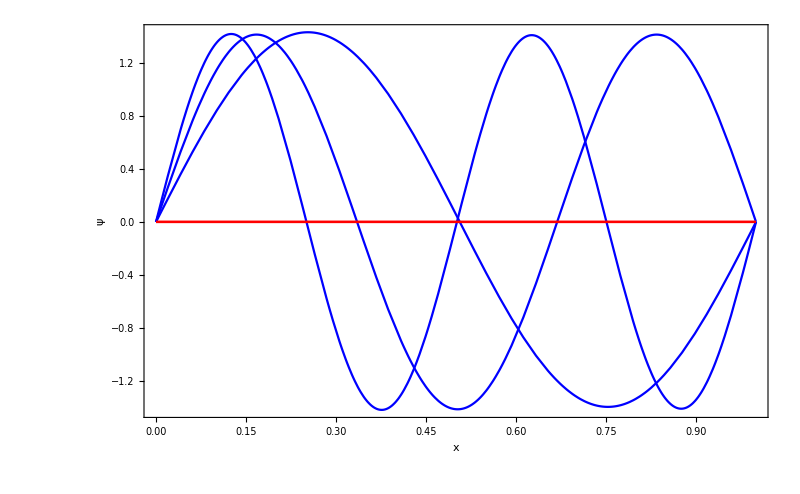

```mathematica
V[x_]:=If[x≤0.5,1,0];
perturbedmodes = GetAccurateModes[TISE,{100,100},{60,60},LBPower->1,UBPower->1];
PrintTable[perturbedmodes,FreqName->"E"]
PrintEigenfunctions[TISE,perturbedmodes⟦2⟧⟦1;;3⟧,60,LBPower->1,UBPower->1,Normalization->"L2Norm"]
```

These values agree well with the analytic solution. Lowering the Cutoff → 2 would reveal the ground state.

```mathematica
NSolve[Sqrt[2(x-1)]Cot[Sqrt[2(x-1)]/2]+Sqrt[2x]Cot[Sqrt[2x]/2]==0&&0≤x≤3*10^4,x,WorkingPrecision->10]
```

{{x→5.42214646},{x→20.24869744},{x→44.91181375},{x→123.8695486},{x→242.3050494},{x→400.2188219},{x→597.6109616},{x→834.481497},{x→1110.830439},{x→1426.657792},{x→1781.963559},{x→2176.747742},{x→2611.01034},{x→3084.751355},{x→3597.970787},{x→4150.668636},{x→4742.844902},{x→5374.499585},{x→6045.632685},{x→6756.244203},{x→7506.334139},{x→8295.902492},{x→9124.949262},{x→9993.47445},{x→10901.47806},{x→11848.96008},{x→12835.92052},{x→13862.35938},{x→14928.27665},{x→16033.67235},{x→17178.54646},{x→18362.89898},{x→19586.72993},{x→20850.03929},{x→22152.82708},{x→23495.09327},{x→24876.83789},{x→26298.06092},{x→27758.76238},{x→29258.94224}}

There are eigenvalues calculated using SpectralBP that does not appear in the list above, like for example 79.4952, 178.1539, 316.3279 and so forth. Using a root finding function around this point, we see that these roots were missed by NSolve.

```mathematica
FindRoot[Sqrt[2(x-1)]Cot[Sqrt[2(x-1)]/2]+Sqrt[2x]Cot[Sqrt[2x]/2]==0,{x,79.5},WorkingPrecision->10]
FindRoot[Sqrt[2(x-1)]Cot[Sqrt[2(x-1)]/2]+Sqrt[2x]Cot[Sqrt[2x]/2]==0,{x,178},WorkingPrecision->10]
FindRoot[Sqrt[2(x-1)]Cot[Sqrt[2(x-1)]/2]+Sqrt[2x]Cot[Sqrt[2x]/2]==0,{x,316},WorkingPrecision->10]
```

{x→79.45920945}

{x→178.1539346}

{x→316.3279345}

The only eigenvalue SpectralBP has missed is the ground state. This is because the nonanalytic behaviour of the ground state is the hardest to capture by the polynomial basis. Recall that the size of the gap of the second derivative of the solution at x = 1/2 is controlled by the difference between unperturbed and perturbed energies.

## Harmonic Oscillator

## Compactifying

Consider the harmonic oscillator potential:

```mathematica
V[x_] := 1/2 x^2;
```

For SpectralBP to work, the domain of the solution must be compact. However, the domain of the harmonic oscillator is [-∞, ∞]. We may compactify this domain with the change of variables : v = Tanh[x], which is a 1 - 1 map of [-∞, ∞] to [-1, 1].
   
By default, SpectralBP assumes the domain of the solution is [0, 1]. We may change this using the options LowerBound and UpperBound, which both default to 0 and 1 respectively. We also note that the wavefunction vanishes at both boundaries.

```mathematica
HOTISE = (TISE /. (ψ -> (ψ2[(Tanh[#])]&))/.x-> ArcTanh[v])//Simplify
HOmodes1 = GetAccurateModes[HOTISE,{100,100},{50,50},LBPower->1,UBPower->1,LowerBound->-1];
PrintTable[HOmodes1,FreqName->"E"]
```

(energy-ArcTanh[v]^2/2) ψ2[v]+v (-1+v^2) ψ2'[v]+1/2 (-1+v^2)^2 ψ2''[v]

Real Eigenvalues |  | 
n | Re E | Im E
1 | 0.5 | 0
2 | 1.5 | 0
3 | 2.5 | 0
4 | 133.1 | 0

Another way of compactifying is using the change of variables v = 1/(1 + Exp[-x]).This maps the interval [-∞,∞] to [0,1].

```mathematica
HOTISE2 = (TISE/. (ψ->(ψ3[(1/(1 + Exp[-#]))]&))/. x -> Log[v/(1-v)])//Simplify
HOmodes2= GetAccurateModes[HOTISE2,{100,100},{50,50},LBPower->1,UBPower->1];
PrintTable[HOmodes2,FreqName->"E"]
```

(energy-1/2 Log[v/(1-v)]^2) ψ3[v]+1/2 (-1+v) v ((-1+2 v) ψ3'[v]+(-1+v) v ψ3''[v])

Real Eigenvalues |  | 
n | Re E | Im E
1 | 0.5 | 0
2 | 1.5 | 0
3 | 2.5 | 0
4 | 3.5 | 0
5 | 4.5 | 0
6 | 5.5 | 0
7 | 6.5 | 0
8 | 7.5 | 0
9 | 8.5 | 0
10 | 9.5 | 0
11 | 10.5 | 0
12 | 11.5 | 0
13 | 12.5 | 0
14 | 13.5 | 0
15 | 14.5 | 0

We see here the dependence of the method on the way we change our variables. Some change of variables are good, while other change of variables are bad.

We may prescribe a weight function in our normalization. By using Normalization → “L2Norm”, we have assumed that the weight function is 1. In our case, we wish to normalize our function in x ∈ [-∞,∞]. We may prescribe a weight function is if it is of the form 

a (u-u_lb)^b(u_ub-u)^c

by specifying Normalization →{“L2Norm”,{a,b,c}}. The change of variables v = 1/(1 + Exp[-x]) gives us a weight function of 1/(v(1-v)), so we use the command Normalization→{“L2Norm”,{1,-1,-1}}.

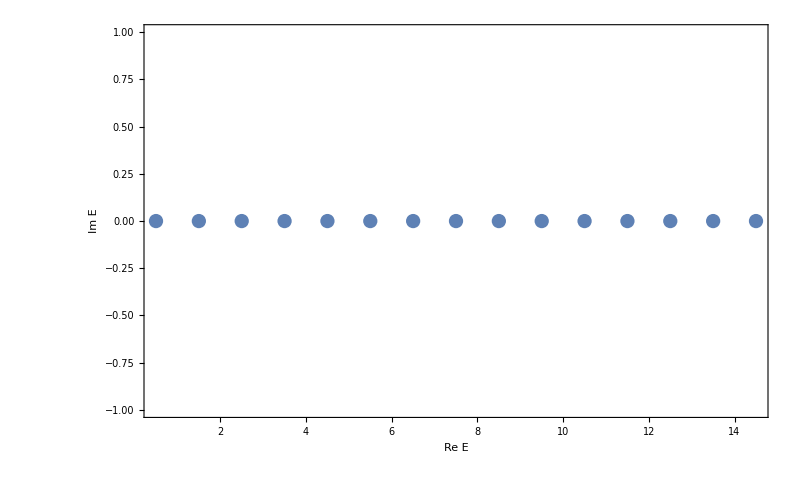
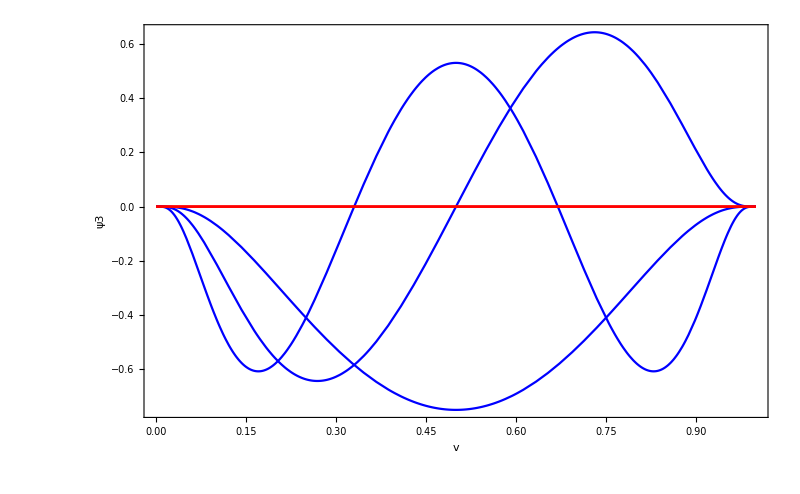
Eigenvalues
-Graphics-
Table of Eigenvalues
Real Eigenvalues |  | 
n | Re E | Im E
1 | 0.5 | 0
2 | 1.5 | 0
3 | 2.5 | 0
4 | 3.5 | 0
5 | 4.5 | 0
6 | 5.5 | 0
7 | 6.5 | 0
8 | 7.5 | 0
9 | 8.5 | 0
10 | 9.5 | 0
11 | 10.5 | 0
12 | 11.5 | 0
13 | 12.5 | 0
14 | 13.5 | 0
15 | 14.5 | 0
Undamped Eigenfunctions
{-Graphics-}

```mathematica
PrintAll[HOTISE2,HOmodes2,50,LBPower->1,UBPower->1,Normalization->{"L2Norm",{1,-1,-1}},FreqName->"E",NEigenFunc->3]
```

## Eigenfunctions

We may extract the eigenfunctions using the command GetEigenfunctions[eqn,spectrum,Nlow,var]. Again, we must specify the various options to recalculate the original matrices from which the spectrum was calculated from.

```mathematica
wavefunctions = GetEigenfunctions[HOTISE2,HOmodes2⟦1,1;;3⟧,100,v,LBPower->1,UBPower->1,Normalization->{"L2Norm",{1,-1,-1}}];
```

We may now revert to the uncompactified domain

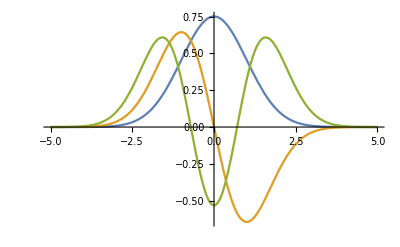

```mathematica
wavefunctions = wavefunctions/.v-> 1/(1+Exp[-x]);
Plot[wavefunctions,{x,-5,5},WorkingPrecision->100]
```

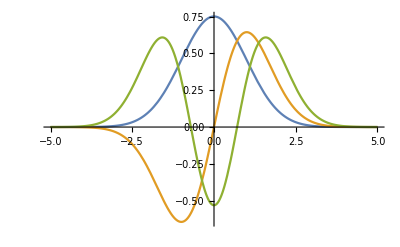

```mathematica
analyticwavefunctions = Table[1/(√(2^n Factorial[n]))π^(-1/4)Exp[-x^2/2]HermiteH[n,x],{n,0,2}];
Plot[analyticwavefunctions,{x,-5,5}]
```

Apart from an overall negative sign, the analytic wavefunctions are very close. For example, comparing the ground states, we get the following error

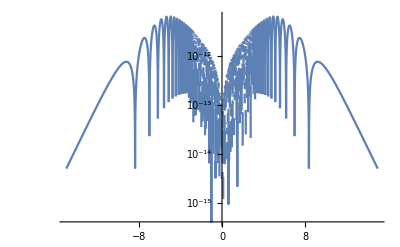

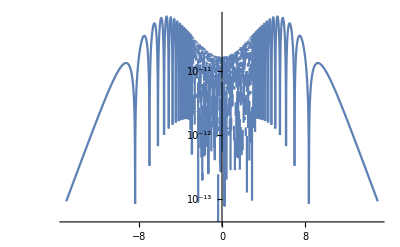

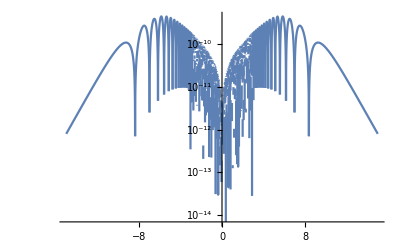

```mathematica
Quiet[LogPlot[Abs[wavefunctions⟦1⟧-analyticwavefunctions⟦1⟧],{x,-15,15},WorkingPrecision->100,PlotRange->All,PlotPoints->200]]
Quiet[LogPlot[Abs[wavefunctions⟦2⟧+analyticwavefunctions⟦2⟧],{x,-15,15},WorkingPrecision->100,PlotRange->All,PlotPoints->200]]
Quiet[LogPlot[Abs[wavefunctions⟦3⟧-analyticwavefunctions⟦3⟧],{x,-15,15},WorkingPrecision->100,PlotRange->All,PlotPoints->200]]
```

## Anharmonic Potential

In both papers we shall try to reconstruct, the momentum operator is normalized such that the TISE is given by

```mathematica
TISE := (energy - V[x])ψ[x] + ψ''[x];
```

#### [1] Numerical evidence that the perturbation expansion for a non-Hermition PT-symmetric Hamiltonian is Stieltjes

There are two anharmonic potentials studied in reference [1]. First we consider the following potential

```mathematica
V[x_]:= 1/4 x^2 + ⅈ λ x^3
```

Again, we compactify

```mathematica
APTISE1= (TISE/. (ψ->(ϕ[(1/(1 + Exp[-#]))]&))/. x -> Log[v/(1-v)])//Simplify
```

(energy-1/4 Log[v/(1-v)]^2-ⅈ λ Log[v/(1-v)]^3) ϕ[v]+(-1+v) v ((-1+2 v) ϕ'[v]+(-1+v) v ϕ''[v])

To recreate Table II of the referenced paper, we set λ →1/7

```mathematica
anharmonicmodes1 = GetAccurateModes[APTISE1/.λ->SetPrecision[1/7,200],{150,150},{200,200},LBPower->1,UBPower->1];
PrintTable[anharmonicmodes1,FreqName->"E"]
```

Real Eigenvalues |  | 
n | Re E | Im E
1 | 0.612738106389 | 0.×10^-104
2 | 2.04730063616 | 0.×10^-103
3 | 3.679862403 | 0.×10^-102
4 | 5.43956942 | 0.×10^-101
5 | 7.296745 | 0.×10^-100
6 | 9.234 | 0.×10^-99
7 | 11.2397 | 0.×10^-98
8 | 13.306 | 0.×10^-97
9 | 15.43 | 0.×10^-96
10 | 1400. | 0.×10^-102
11 | 1592. | 0.×10^-104

For a direct comparison with Table II, we use Equation (9) from [1] to get

```mathematica
Egroundstate11 = anharmonicmodes1⟦1,1⟧;
Egroundstate12 = anharmonicmodes1⟦2,1⟧;
Pλ1 = {{7^2(Egroundstate11 -1/2)},{7^2(Egroundstate12 -1/2)}};
PrintTable[Pλ1,FreqName->"P(λ^2)"]
```

Real Eigenvalues |  | 
n | Re P(λ^2) | Im P(λ^2)
1 | 5.52416721306 | 0.×10^-102

We may calculate the eigenfunctions

```mathematica
wavefunctions1 = GetEigenfunctions[APTISE1/.λ->SetPrecision[1/7,150],anharmonicmodes1⟦2,1;;3⟧,150,v,LBPower->1,UBPower->1,Normalization->{"L2Norm",{1,-1,-1}}];
```

Returning to our original coordinate system, we get

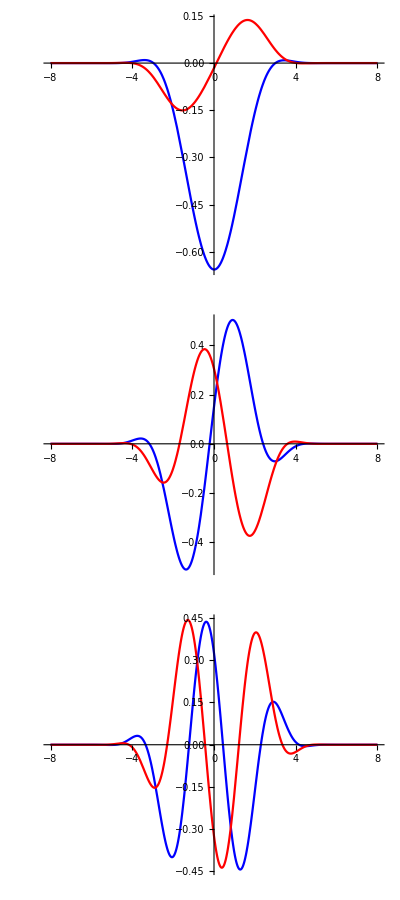

```mathematica
wavefunctions1 =wavefunctions1/.v-> 1/(1+Exp[-x]);
Grid[Quiet[Table[{Plot[{Re[wavefunctions1⟦k⟧],Im[wavefunctions1⟦k⟧]},{x,-8,8},WorkingPrecision->150,PlotStyle->{{Blue},{Red}},ImageSize->400,PlotRange->All]},{k,3}]],Frame->All]
```

The other potential considered in [1] is given by

```mathematica
V[x_]:=x^2+ β x^4
```

Compactifying

```mathematica
APTISE2= (TISE/. (ψ->(ϕ[(1/(1 + Exp[-#]))]&))/. x -> Log[v/(1-v)])//Simplify
```

(energy-Log[v/(1-v)]^2-β Log[v/(1-v)]^4) ϕ[v]+(-1+v) v ((-1+2 v) ϕ'[v]+(-1+v) v ϕ''[v])

To recreate Table II of the referenced paper, we set β → 40/49.

```mathematica
anharmonicmodes2 = GetAccurateModes[APTISE2/.β->SetPrecision[40/49,100],{50,50},{100,100},LBPower->1,UBPower->1];
PrintTable[anharmonicmodes2,FreqName->"E"]
```

Real Eigenvalues |  | 
n | Re E | Im E
1 | 1.34224442125182 | 0
2 | 4.4523757367164 | 0
3 | 8.244544675014 | 0
4 | 12.49407778264 | 0
5 | 17.11263824818 | 0
6 | 22.045402676 | 0
7 | 27.254591456 | 0
8 | 32.71221323 | 0
9 | 38.3965175 | 0
10 | 44.290014 | 0
11 | 50.378269 | 0
12 | 56.649128 | 0
13 | 63.09218 | 0
14 | 69.6984 | 0
15 | 76.4599 | 0
16 | 83.3696 | 0
17 | 90.421 | 0
18 | 97.61 | 0
19 | 104.93 | 0
20 | 112.4 | 0
21 | 119.9 | 0
22 | 127.6 | 0
23 | 135. | 0

For a direct comparison with Table II, we use Equation (8) from [1] to get

```mathematica
Egroundstate21 = anharmonicmodes2⟦1,1⟧;
Egroundstate22 = anharmonicmodes2⟦2,1⟧;
Pλ2 = {{(49/40)(Egroundstate21 -1)},{(49/40)(Egroundstate22 -1)}};
PrintTable[Pλ2,FreqName->"P(λ^2)"]
```

Real Eigenvalues |  | 
n | Re P(λ^2) | Im P(λ^2)
1 | 0.41924941603348 | 0

We may also calculate the eigenfuncitons

```mathematica
wavefunctions2 = GetEigenfunctions[APTISE2/.β->SetPrecision[40/49,50],anharmonicmodes2⟦2,1;;3⟧,50,v,LBPower->1,UBPower->1,Normalization->{"L2Norm",{1,-1,-1}}];
```

Returning to our original coordinate system, we get

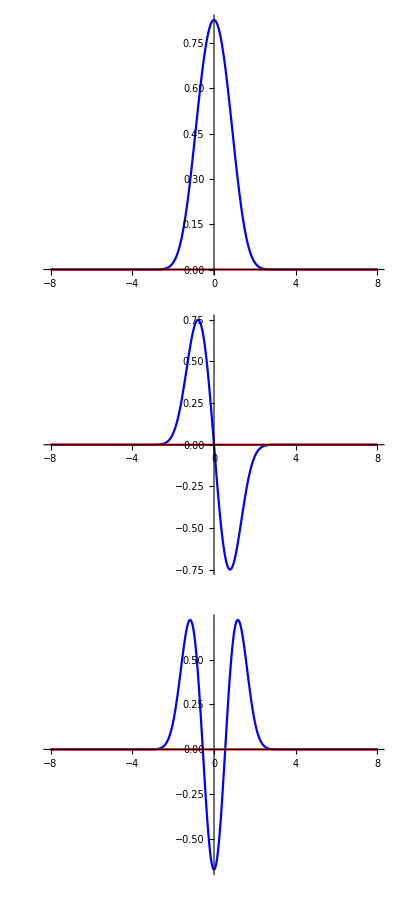

```mathematica
wavefunctions2 =wavefunctions2/.v-> 1/(1+Exp[-x]);
Grid[Quiet[Table[{Plot[{Re[wavefunctions2⟦k⟧],Im[wavefunctions2⟦k⟧]},{x,-8,8},WorkingPrecision->50,PlotStyle->{{Blue},{Red}},ImageSize->400,PlotRange->All]},{k,3}]],Frame->All]
```

#### [2] Notes on the Pade Approximation for an Anharmonic Oscillator

In [2], an identical potential is used in [1]. They calculated the groundstate energies at β = 0.1, 0.2, 1.0, 10.0, 100.0. We do the same here

```mathematica
anharmonicmodes3 = GetAccurateModes[APTISE2/.β->SetPrecision[1/10,200],{150,150},{200,200},LBPower->1,UBPower->1];//Timing
PrintTable[anharmonicmodes3,FreqName->"E"]
```

{71.3906,Null}

Real Eigenvalues |  | 
n | Re E | Im E
1 | 1.0652855095437176888570916288 | 0
2 | 3.3068720131529135071281217 | 0
3 | 5.747959268833563304733503 | 0
4 | 8.3526778257857547121553 | 0
5 | 11.098595622633043011086 | 0
6 | 13.96992619774279930097 | 0
7 | 16.95479468614415133769 | 0
8 | 20.0438636041884612336 | 0
9 | 23.229552179939289071 | 0
10 | 26.50555475253661742 | 0
11 | 29.866525234671278 | 0
12 | 33.307860594219915 | 0
13 | 36.825546715516142 | 0
14 | 40.41604532291638 | 0
15 | 44.0762089252941 | 0
16 | 47.803215466666 | 0
17 | 51.59451719475 | 0
18 | 55.447800016366 | 0
19 | 59.3609507376 | 0
20 | 63.3320303334 | 0
21 | 67.359251897 | 0
22 | 71.440962269 | 0
23 | 75.5756266 | 0
24 | 79.7618153 | 0
25 | 83.9981928 | 0
26 | 88.2835079 | 0
27 | 92.616586 | 0
28 | 96.996321 | 0
29 | 101.42167 | 0
30 | 105.89165 | 0
31 | 110.40532 | 0
32 | 114.9618 | 0
33 | 119.56 | 0
34 | 124.2 | 0
35 | 128.87986 | 0
36 | 133.6 | 0
37 | 138.36 | 0
38 | 143.16 | 0
39 | 147.99 | 0
40 | 152.9 | 0
41 | 157.8 | 0
42 | 162.7 | 0
43 | 167.7 | 0
44 | 182.8 | 0
45 | 204. | 0
46 | 1240. | 0
47 | 1810. | 0

```mathematica
anharmonicmodes4 = GetAccurateModes[APTISE2/.β->SetPrecision[2/10,200],{150,150},{200,200},LBPower->1,UBPower->1];//Timing
PrintTable[anharmonicmodes4,FreqName->"E"]
```

{70.8594,Null}

Real Eigenvalues |  | 
n | Re E | Im E
1 | 1.11829265436703915343081315384 | 0
2 | 3.539005287898108489146307897 | 0
3 | 6.27724861699624086905437128 | 0
4 | 9.25776561777628348933970222 | 0
5 | 12.440601800013043756778043 | 0
6 | 15.79953445574285240704033 | 0
7 | 19.3156799843202920317419 | 0
8 | 22.974631158888411333855 | 0
9 | 26.76494961489154062292 | 0
10 | 30.67728407899001892142 | 0
11 | 34.703815271428031823 | 0
12 | 38.83788672911345078 | 0
13 | 43.07374853857925245 | 0
14 | 47.4063732172589127 | 0
15 | 51.831319630096689 | 0
16 | 56.344629991745466 | 0
17 | 60.94275031778635 | 0
18 | 65.6224679057219 | 0
19 | 70.3808614475602 | 0
20 | 75.2152606860863 | 0
21 | 80.123213399988 | 0
22 | 85.10245809893 | 0
23 | 90.1509012251 | 0
24 | 95.2665979535 | 0
25 | 100.447735895 | 0
26 | 105.692621167 | 0
27 | 110.9996664 | 0
28 | 116.36738039 | 0
29 | 121.79435901 | 0
30 | 127.2792774 | 0
31 | 132.820883 | 0
32 | 138.417989 | 0
33 | 144.06947 | 0
34 | 149.77426 | 0
35 | 155.5313 | 0
36 | 161.3397 | 0
37 | 167.19849 | 0
38 | 173.107 | 0
39 | 179.064 | 0
40 | 185.068 | 0
41 | 191.1203 | 0
42 | 197.22 | 0
43 | 203.36 | 0
44 | 209.55 | 0
45 | 215.8 | 0
46 | 222.1 | 0
47 | 228. | 0
48 | 234.7 | 0
49 | 1240. | 0
50 | 1807. | 0

```mathematica
anharmonicmodes5 = GetAccurateModes[APTISE2/.β->SetPrecision[1,200],{150,150},{200,200},LBPower->1,UBPower->1];//Timing
PrintTable[anharmonicmodes5,FreqName->"E"]
```

{70.1094,Null}

Real Eigenvalues |  | 
n | Re E | Im E
1 | 1.39235164153029185565750787660993418 | 0
2 | 4.6488127042120775363770329172605845 | 0
3 | 8.655049957759309688116539457377308 | 0
4 | 13.15680389804987507920977204038231 | 0
5 | 18.057557436303252894771239646525 | 0
6 | 23.2974414512231890848644819921 | 0
7 | 28.8353384595042488401336357155 | 0
8 | 34.640848321111332542884527618 | 0
9 | 40.690386082106444725278931482 | 0
10 | 46.965009505675527984096443324 | 0
11 | 53.4491021396652646008315065 | 0
12 | 60.129522959157771315848016 | 0
13 | 66.9950300012471660610197 | 0
14 | 74.0358743591025301807412 | 0
15 | 81.2435050507671527370665 | 0
16 | 88.610348800799158873039 | 0
17 | 96.12964204523405204681 | 0
18 | 103.7953003222726096781 | 0
19 | 111.6018150451729585337 | 0
20 | 119.54417073305031113 | 0
21 | 127.617777795354918334 | 0
22 | 135.81841732561037334 | 0
23 | 144.1421952963981637 | 0
24 | 152.5855042055739216 | 0
25 | 161.1449906945129519 | 0
26 | 169.81752800159535 | 0
27 | 178.60019236687576 | 0
28 | 187.4902426929503 | 0
29 | 196.48510291022044 | 0
30 | 205.582346604424 | 0
31 | 214.779683549177 | 0
32 | 224.0749478526 | 0
33 | 233.46608747938 | 0
34 | 242.9511549511 | 0
35 | 252.5282990615 | 0
36 | 262.195757469 | 0
37 | 271.95185005 | 0
38 | 281.79497292 | 0
39 | 291.72359305 | 0
40 | 301.7362434 | 0
41 | 311.83151827 | 0
42 | 322.00807 | 0
43 | 332.264604 | 0
44 | 342.599876 | 0
45 | 353.01269 | 0
46 | 363.50189 | 0
47 | 374.0664 | 0
48 | 384.70507 | 0
49 | 395.4169 | 0
50 | 406.201 | 0
51 | 417.056 | 0
52 | 427.9818 | 0
53 | 438.98 | 0
54 | 450.04 | 0
55 | 461.17 | 0
56 | 472.37 | 0
57 | 483.6 | 0
58 | 495. | 0
59 | 506.4 | 0
60 | 518. | 0
61 | 540.9 | 0
62 | 1179. | 0
63 | 2050. | 0

```mathematica
anharmonicmodes6 = GetAccurateModes[APTISE2/.β->SetPrecision[10,200],{150,150},{200,200},LBPower->1,UBPower->1];//Timing
PrintTable[anharmonicmodes6,FreqName->"E"]
```

{70.7969,Null}

Real Eigenvalues |  | 
n | Re E | Im E
1 | 2.449174072118386918268793906187730426220277999 | 0
2 | 8.59900345480777260276499024450967003375394393 | 0
3 | 16.63592149241375778336191793219245762382339 | 0
4 | 25.80627621505564044972657890169049352735961 | 0
5 | 35.8851712222538737122812690981911859061321 | 0
6 | 46.729080900817113005813013742850484494624 | 0
7 | 58.24129873975324028510421765441069611828 | 0
8 | 70.3510519392346533089600813017152402078 | 0
9 | 83.0038670375852900204307960933915570699 | 0
10 | 96.15626298119775969323854462328080451 | 0
11 | 109.7725708643329749736738798372486135 | 0
12 | 123.822898910159159705762812280457833 | 0
13 | 138.28176347095463822201027567297664 | 0
14 | 153.127130748369123353508182978031 | 0
15 | 168.3397239621575374324311630426973 | 0
16 | 183.902508794209186902225748664247 | 0
17 | 199.80030246219770641806634258302 | 0
18 | 216.01947088996515926390423385745 | 0
19 | 232.5476901382481471873278172535 | 0
20 | 249.373755670188058532352403893 | 0
21 | 266.4874278646408186039176507 | 0
22 | 283.8793054334074236488118868 | 0
23 | 301.540720623104002679075949 | 0
24 | 319.463651640041922198015667 | 0
25 | 337.64064884739992546443299 | 0
26 | 356.0647720895021023223178 | 0
27 | 374.72953709093921328659074 | 0
28 | 393.6288693206963153407671 | 0
29 | 412.757064045718242594511 | 0
30 | 432.10875155380190163459 | 0
31 | 451.67886672299910244166 | 0
32 | 471.4626222685782802449 | 0
33 | 491.455485119675266711 | 0
34 | 511.653155473849109835 | 0
35 | 532.0515481546069197326 | 0
36 | 552.6467759588737076 | 0
37 | 573.4351347316040932 | 0
38 | 594.4130899457322838 | 0
39 | 615.577264599330446 | 0
40 | 636.92442826965998 | 0
41 | 658.45148718689823 | 0
42 | 680.15547520960194 | 0
43 | 702.0335456001372 | 0
44 | 724.082963511927 | 0
45 | 746.301099111895 | 0
46 | 768.68542127127 | 0
47 | 791.23349176628 | 0
48 | 813.9429599374 | 0
49 | 836.81155776196 | 0
50 | 859.8370953 | 0
51 | 883.01745648 | 0
52 | 906.350595187 | 0
53 | 929.83453164 | 0
54 | 953.467349 | 0
55 | 977.2471902 | 0
56 | 1001.1722552 | 0
57 | 1025.240798 | 0
58 | 1049.451124 | 0
59 | 1073.801588 | 0
60 | 1098.29059 | 0
61 | 1122.91658 | 0
62 | 1147.67805 | 0
63 | 1172.5735 | 0
64 | 1197.6016 | 0
65 | 1222.7608 | 0
66 | 1248.05 | 0
67 | 1273.467 | 0
68 | 1299.012 | 0
69 | 1324.68 | 0
70 | 1350.48 | 0
71 | 1376.4 | 0
72 | 1402.4 | 0
73 | 1428.6 | 0
74 | 1454.9 | 0
75 | 1481. | 0
76 | 1508. | 0
77 | 1534. | 0
78 | 1561. | 0
79 | 1588. | 0
80 | 1670. | 0
81 | 2120. | 0

```mathematica
anharmonicmodes7 = GetAccurateModes[APTISE2/.β->SetPrecision[100,200],{150,150},{200,200},LBPower->1,UBPower->1];//Timing
PrintTable[anharmonicmodes7,FreqName->"E"]
```

{69.5625,Null}

Real Eigenvalues |  | 
n | Re E | Im E
1 | 4.99941754513758782929463203734965271862550738578 | 0
2 | 17.8301927159525223865570295362908864378631444701 | 0
3 | 34.873984261994777546412103561207086574032961456 | 0
4 | 54.3852915716031032689477663763430497545628983 | 0
5 | 75.877004028669724180840011902916125091111793 | 0
6 | 99.03283731540749122796780175192058537362834 | 0
7 | 123.6406976266781676741109654643608147181306 | 0
8 | 149.5456574432882211736014873678644598884764 | 0
9 | 176.62865595771435360360472819344492824245 | 0
10 | 204.7947745129447031957215597095780825746 | 0
11 | 233.966225876235944863913218792906733297 | 0
12 | 264.077875648485826150184101005421448814 | 0
13 | 295.07423370290048629095345520140308667 | 0
14 | 326.9073507856682946724905348107600938 | 0
15 | 359.535299358580767658053985307926346 | 0
16 | 392.92104637156935055305546494331667 | 0
17 | 427.03159755666960867059107730772503 | 0
18 | 461.8373350322606214744818027388767 | 0
19 | 497.311495801412903692831338825163 | 0
20 | 533.42975505546576154884916682407 | 0
21 | 570.16988884453986832657762785949 | 0
22 | 607.511497809530761665067946471 | 0
23 | 645.43577855923161211311248264 | 0
24 | 683.92533269722196807207975301 | 0
25 | 722.964005941463644360782728 | 0
26 | 762.536751546556262617784945 | 0
27 | 802.629513538541453555145047 | 0
28 | 843.22912624164178939180272 | 0
29 | 884.3232273084700875110087 | 0
30 | 925.9001820245304132372889 | 0
31 | 967.949017089603251312829 | 0
32 | 1010.459362415204479770884 | 0
33 | 1053.42139974209306293437 | 0
34 | 1096.8258170918542453631 | 0
35 | 1140.6637682345272391972 | 0
36 | 1184.926836489506549128 | 0
37 | 1229.60700228663282714 | 0
38 | 1274.696614003911028789 | 0
39 | 1320.1883616718005232 | 0
40 | 1366.07525319472314 | 0
41 | 1412.3505927908316492 | 0
42 | 1459.00796139313512 | 0
43 | 1506.04119879033904 | 0
44 | 1553.44438731545906 | 0
45 | 1601.211836915393 | 0
46 | 1649.338071455979 | 0
47 | 1697.817816135269 | 0
48 | 1746.64598589332 | 0
49 | 1795.8176747202 | 0
50 | 1845.3281457755 | 0
51 | 1895.172822242 | 0
52 | 1945.347278847 | 0
53 | 1995.84723399 | 0
54 | 2046.66854241 | 0
55 | 2097.8071884 | 0
56 | 2149.2592794 | 0
57 | 2201.0210401 | 0
58 | 2253.088807 | 0
59 | 2305.459023 | 0
60 | 2358.128232 | 0
61 | 2411.09308 | 0
62 | 2464.3503 | 0
63 | 2517.8967 | 0
64 | 2571.729 | 0
65 | 2625.8448 | 0
66 | 2680.241 | 0
67 | 2734.914 | 0
68 | 2789.86 | 0
69 | 2845.08 | 0
70 | 2900.57 | 0
71 | 2956.3 | 0
72 | 3012.3 | 0
73 | 3068.6 | 0
74 | 3125. | 0
75 | 3182. | 0
76 | 3239. | 0
77 | 3296. | 0
78 | 19200. | 0
79 | 19200. | 0

Our calculations agree with their results to a high degree. Where the digits disagree, it is within the error bars of the “Exact” values [2] provides in Tables II and IV.

## References

[1] Bender, C. M., & Weniger, E. J. (2001). Numerical evidence that the perturbation expansion for a non-Hermitian PT-symmetric Hamiltonian is Stieltjes. Journal of Mathematical Physics, 42(5), 2167. doi:10.1063/1.1362287
[2] Ezawa, H., Saito, M., & Nakamura, T. (2014). Notes on the Padé Approximation for an Anharmonic Oscillator. Journal of the Physical Society of Japan, 83(3), 034003. doi:10.7566/jpsj.83.034003